```mathematica
data=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data (processed by age and gender).csv"];
```

Initializing Semantic Import indices ....

```mathematica
SynthesizeMissingValues[data]
```

```mathematica
ProgressIndicator[Dynamic[i],{3,77}]
```

```mathematica
data2=Table[Values[Transpose[Normal[SynthesizeMissingValues[Normal[data[All,{2,i}]],Method-><|"LearningMethod"->"KernelDensityEstimation", "EvaluationStrategy"->"ModeFinding"|>,PerformanceGoal->"Quality"]]]⟦2⟧],{i,3,77}];
```

```mathematica
Export["data standardized.csv",Standardize[Transpose[data2]]]
```

data standardized.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["data standardized.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["processed data by age.csv"]]]
```

```mathematica
ld=LearnDistribution[Normal[data[All,{2,75}]],Method->"KernelDensityEstimation"]
```

LearnedDistribution[…]

```mathematica
RandomVariate[ld]
```

<|age→76.4399,Antithrombin→81.1136|>

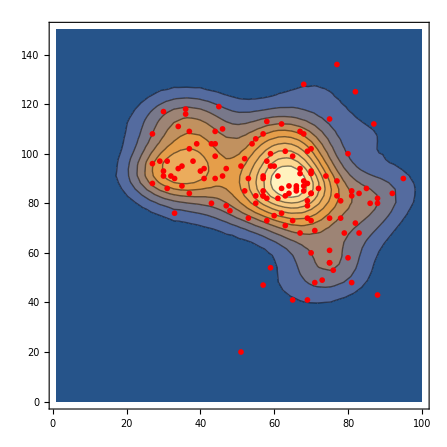

```mathematica
Show[ContourPlot[PDF[ld,{x,y}],{x,1,100},{y,0,150},PlotRange->All,Contours->10],ListPlot[Normal[data[All,{2,75}]], PlotStyle->Red]]
```

```mathematica
ProgressIndicator[Dynamic[i],{4,77}]
```

```mathematica
data3=Table[Values[Transpose[Normal[SynthesizeMissingValues[Normal[data[All,{2,3,i}]],Method-><|"LearningMethod"->"KernelDensityEstimation", "EvaluationStrategy"->"ModeFinding"|>,PerformanceGoal->"Quality"]]]⟦3⟧],{i,4,77}];
```

```mathematica
Export["processed data by age and gender.csv",Transpose[data3]]
```

processed data by age and gender.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["processed data by age and gender.csv"]]]
```

## Up/down regulated

```mathematica
data=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data (processed by age and gender).csv"];
```

```mathematica
normalized=Normalize[Normal[data]];
```

```mathematica
Normal[data[All,1]]
```

{2,3,5,7,8,9,11,12,13,15,18,19,21,22,24,26,27,28,31,32,33,40,43,44,47,52,60,61,63,65,66,67,70,71,73,75,77,79,82,83,85,86,88,90,91,92,94,96,97,98,104,105,107,108,113,117,125,128,129,135,137,139,141,142,144,145,146,147,148,149,152,155,156,158,159,160,161,162,164,165,166,168,169,170,171,172,173,174,175,176,177,178,182,183,193,194,195,196,199,203,204,205,207,210,211,212,216,217,219,220,221,222,224,226,227,228,229,231,232,234,235,237,238,239,240,243,244,246,250,256,258,260,261,262,263,264,267,273,278,281,282,283,288,291,292,295,296,304,306,308,309,313,315,320,322,324,326,328,332,337,338,339,341,343,344,348,349,352,358,361,362,364,368,372,374,375}

```mathematica
Normalize[Normal[data[All,4]]]
```

{0.0060475,0.00493727,0.00566871,0.00496339,0.0129309,0.0291273,0.00616505,0.00594301,0.0134534,0.00515931,0.00466297,0.00372254,0.0058777,0.00653077,0.00425807,0.00581239,0.00479359,0.00576014,0.00496339,0.00378785,0.00642628,0.00732753,0.00471522,0.00528993,0.00624342,0.0054336,0.005094,0.00404908,0.00501564,0.00326539,0.00542054,0.00544667,0.00534217,0.00501564,0.00513319,0.00450623,0.00378785,0.00731447,0.00666139,0.00940432,0.00235108,0.00508094,0.00545973,0.01698,0.00583851,0.00966555,0.00467603,0.00574708,0.00849001,0.00835939,0.0045193,0.00508094,0.0144983,0.00770631,0.0060475,0.000130615,0.00470216,0.00783693,0.0045846,0.0545973,0.0120166,0.00404908,0.00658302,0.00455848,0.00483277,0.00195923,0.00626954,0.00532911,0.00607362,0.00404908,0.00582545,0.00501564,0.00535524,0.00480665,0.001698,0.00594301,0.00527687,0.00696181,0.00595607,0.00457154,0.0068965,0.00472828,0.00527687,0.00130615,0.0438868,0.0044148,0.0055381,0.00531605,0.00513319,0.00544667,0.00535524,0.0054336,0.00632179,0.004245,0.00561647,0.00427113,0.0062173,0.00497645,0.00694874,0.00548585,0.00480665,0.00386622,0.00612587,0.00497645,0.00603444,0.00590382,0.00513319,0.00206372,0.00670057,0.00445399,0.00429725,0.0033307,0.04245,0.0043495,0.00549891,0.00501564,0.00463685,0.00497645,0.00540748,0.00646547,0.00474134,0.00455848,0.00484583,0.00624342,0.00513319,0.00318702,0.00335682,0.00510707,0.00578627,0.00561647,0.00462379,0.00564259,0.00377479,0.00559034,0.00476747,0.00534217,0.00466297,0.00472828,0.00470216,0.00454542,0.00581239,0.00596913,0.00505482,0.00589076,0.00476747,0.00436256,0.00104492,0.00480665,0.0054336,0.00521156,0.00472828,0.978963,0.0065569,0.00394459,0.00531605,0.00385316,0.0892104,0.00530299,0.0046891,0.142893,0.00484583,0.00591688,0.0057732,0.00552504,0.00557728,0.00538136,0.0040099,0.00901247,0.00557728,0.0047544,0.00566871,0.00489808,0.0044148,0.00437562,0.00514625,0.00641322}

```mathematica
normalized[All,1]//Normal
```

{<|PATIENT_ID→2/(√7631601),age→61/(7 √13318),gender→1/(√389),72,Fibrin (pro) degradation products→0.0112286,Outcome→0|>,<|PATIENT_ID→√(3/2543867),age→5 √(2/6659),gender→2/(√389),72,Fibrin (pro) degradation products→0.00469468,Outcome→0|>,172,<|PATIENT_ID→374/(√7631601),age→33/(7 √13318),73,Fibrin (pro) degradation products→0.17605,Outcome→1/(√77)|>,<|PATIENT_ID→125 √(3/2543867),age→(34 √(2/6659))/7,gender→1/(√389),72,Fibrin (pro) degradation products→0.00645518,Outcome→1/(√77)|>}[All,1]
 |  |  |  |

```mathematica
regulatedData=Table[N[Normalize[Normal[data[All,i]]]-ConstantArray[Mean[Normalize[Normal[data[All,i]]]],176]],{i,4,76}];
```

```mathematica
regulatedData//Dimensions
```

{73,176}

```mathematica
Export["regulated1.csv",Transpose[regulatedData]]
```

regulated1.csv

```mathematica
regulated=Table[N[Normal[data[All,k]]-ConstantArray[Median[Normal[data[All,k]]],176]],{k,4,76}];
```

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{261,Missing[Unrecognized,221.1],292,97,315,315,183,244,221,273,217,Missing[Unrecognized,194.4],267,262,153,415,246,Missing[Unrecognized,344.6],223,213,391,Missing[Unrecognized,307.2],Missing[Unrecognized,268.2],Missing[Unrecognized,474.7],Missing[Unrecognized,398.3],Missing[Unrecognized,243.4],167,278,216,334,214,195,454,319,300,289,290,437,264,224,195,322,229,260,224,400,294,166,300,248,«126»}].

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{261.,Missing[Unrecognized,221.1],292.,97.,315.,315.,183.,244.,221.,273.,217.,Missing[Unrecognized,194.4],267.,262.,153.,415.,246.,Missing[Unrecognized,344.6],223.,213.,391.,Missing[Unrecognized,307.2],Missing[Unrecognized,268.2],Missing[Unrecognized,474.7],Missing[Unrecognized,398.3],Missing[Unrecognized,243.4],167.,278.,216.,334.,214.,195.,454.,319.,300.,289.,290.,437.,264.,224.,195.,322.,229.,260.,224.,400.,294.,166.,300.,248.,«126»}].

General::stop: Further output of Median::rectn will be suppressed during this calculation.

```mathematica
Export["regulated.csv",regulated]
```

regulated.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["regulated.csv"]]]
```

```mathematica
regulated//Dimensions
```

{73,176,176}

```mathematica
regulated
```

$Aborted[]

```mathematica
Normal[data[[All,2]]]-ConstantArray[Normal[data[[All,2]]],176]
```

```mathematica
N[Normalize[Normal[data[All,4]]]-ConstantArray[Median[Normalize[Normal[data[All,4]]]],176]]
```

{0.000751039,-0.000359193,0.000372254,-0.00033307,0.00763448,0.0238308,0.000868593,0.000646547,0.00815694,-0.000137146,-0.000633485,-0.00157392,0.000581239,0.00123432,-0.00103839,0.000515931,-0.00050287,0.000463685,-0.00033307,-0.00150861,0.00112982,0.00203107,-0.000581239,-6.53077×10^-6,0.000946962,0.000137146,-0.000202454,-0.00124738,-0.000280823,-0.00203107,0.000124085,0.000150208,0.0000457154,-0.000280823,-0.000163269,-0.000790224,-0.00150861,0.00201801,0.00136493,0.00410786,-0.00294538,-0.000215516,0.000163269,0.0116836,0.000542054,0.00436909,-0.000620424,0.000450623,0.00319355,0.00306293,-0.000777162,-0.000215516,0.00920186,0.00240986,0.000751039,-0.00516584,-0.000594301,0.00254047,-0.000711854,0.0493008,0.00672017,-0.00124738,0.00128656,-0.000737978,-0.000463685,-0.00333723,0.000973085,0.0000326539,0.000777162,-0.00124738,0.000528993,-0.000280823,0.000058777,-0.000489808,-0.00359846,0.000646547,-0.0000195923,0.00166535,0.000659608,-0.000724916,0.00160004,-0.000568177,-0.0000195923,-0.0039903,0.0385903,-0.000881655,0.000241639,0.0000195923,-0.000163269,0.000150208,0.000058777,0.000137146,0.00102533,-0.00105145,0.000320008,-0.00102533,0.000920839,-0.000320008,0.00165229,0.000189392,-0.000489808,-0.00143024,0.000829408,-0.000320008,0.000737978,0.000607362,-0.000163269,-0.00323273,0.00140412,-0.00084247,-0.000999209,-0.00196576,0.0371536,-0.000946962,0.000202454,-0.000280823,-0.000659608,-0.000320008,0.000111023,0.00116901,-0.000555116,-0.000737978,-0.000450623,0.000946962,-0.000163269,-0.00210944,-0.00193964,-0.000189392,0.000489808,0.000320008,-0.00067267,0.000346131,-0.00152167,0.000293885,-0.000528993,0.0000457154,-0.000633485,-0.000568177,-0.000594301,-0.000751039,0.000515931,0.00067267,-0.000241639,0.000594301,-0.000528993,-0.000933901,-0.00425153,-0.000489808,0.000137146,-0.0000849001,-0.000568177,0.973667,0.00126044,-0.00135187,0.0000195923,-0.0014433,0.0839139,6.53077×10^-6,-0.000607362,0.137597,-0.000450623,0.000620424,0.000476747,0.000228577,0.000280823,0.0000849001,-0.00128656,0.00371601,0.000280823,-0.000542054,0.000372254,-0.000398377,-0.000881655,-0.000920839,-0.000150208,0.00111676}

```mathematica
data=Import["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data (processed by age and gender).csv"];
data=data[[2;;177,4;;76]];
data=Transpose[Table[N[Normalize[data[[All,k]]]],{k,1,73}]];
Export["data normalized.csv",data]
```

data normalized.csv

```mathematica
SystemOpen["data normalized.csv"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["data normalized.csv"]]]
```

```mathematica
Dimensions[%]
```

{73,176}

```mathematica
data//Dimensions
```

{176,73}

```mathematica
data1
```

```mathematica
data[[All,2]]
```

{10.37,7.68,7.95,9.52,19.4,231.4,4.72,4.87,229.4,6.09,5.31,2.42,7.29,8,5.17,4.21,4.72,4.46,4.47,1,14.92,6.26,5.54,5.53,6.74,3.56,4.66,4.8,3.76,13.2,6.54,4.73,5.28,3.85,3.93,5.38,3.5,18.7,4.1,16.3,5.5,4.58,10.92,4.6,5.33,2,6.88,8.95,3.6,6.7,4.43,4.75,10.1,10.3,11.26,0.8,6.8,3.4,4.19,9.2,4.1,1726.6,7.34,3.39,5.41,9.4,12.2,8.04,8.55,3,3.86,5.08,24.4,4.93,1.5,4.57,5.32,5.73,6.86,4.39,6.5,5.92,3.21,14.6,8.8,5.17,6.92,7.16,9.86,9.45,4.84,9.51,5.24,4.57,20.22,12.05,6.17,6.57,15.15,11.08,12.44,13,12.49,25.49,5.56,4.33,26.36,6.55,23.16,28.06,29.71,0.8,16.3,10,9.34,15.12,7.92,7.99,8.32,16.39,19.71,24.82,13.8,13.42,16.81,0.71,11,16.85,8.52,6.84,9.94,3.3,34.84,12.26,20.05,10.05,18.07,6.57,24.64,2.69,27.2,20.77,18.04,14.32,3.92,2.17,2.1,18.55,10.97,4.94,31.73,63.2,10.17,4.22,10.49,16.65,11.4,6.87,18.69,605.8,14.53,10.55,9.54,32.99,19.07,15.97,12.27,3.4,5.56,5.79,10.2,11.5,31.8,28.04,14.49,8.25}